# Hyperfine splitting of Cesium 133

## César Muro Cabral

We investigate the hyperfine splitting of Cesium133 with a flux of magnetic field. We assume magnetic field Bz is in z-direction.
Let us first obtain the plot for the ground state 6 S_(1/2). The nuclear spin magnetic moment of Cesium es I=7/2.
We need to define matrices for a given general Spin S. We have to realize that for a given spin S, there are{2S+1,2S+1} matrix elements. Then we define the matrices for S_- and S_+, and with them we define also the matrices for S_x, S_y, and S_z.

```mathematica
SpinQ[S_]:=IntegerQ[2S]&&S≥0
splus[0]={{0}}//SparseArray;
splus[S_?SpinQ]:=splus[S]= SparseArray[Band[{1,2}]->Table[Sqrt[S(S+1)-M(M+1)],{M,S-1,-S,-1}],{2S+1,2S+1}]
sminus[S_?SpinQ]:=Transpose[splus[S]]
sx[S_?SpinQ]:=sx[S]=(splus[S]+sminus[S])/2
sy[S_?SpinQ]:=sy[S]=(splus[S]-sminus[S])/(2I)
sz[S_?SpinQ]:=sz[S]=SparseArray[Band[{1,1}]->Range[S,-S,-1],{2S+1,2S+1}]
id[S_?SpinQ]:=id[S]=IdentityMatrix[2S+1,SparseArray]
```

```mathematica
EnergyUnit=Quantity["PlanckConstant"]*Quantity["Gigahertz"];
TimeUnit=Quantity["Microseconds"];
```

```mathematica
MagneticFieldUnit=Quantity["Gausses"];
μB=Quantity["BohrMagneton"]/(EnergyUnit/MagneticFieldUnit)//UnitConvert;
```

```mathematica
ℏn=Quantity["ReducedPlanckConstant"]/(EnergyUnit*TimeUnit);
```

```mathematica
μBn=Quantity["BohrMagneton"]/(EnergyUnit/MagneticFieldUnit);
```

Since for this level the atom has I=7/2, J=1/2  (L=0, S=1/2), the basis for the description is the tensor product of a Spin(7/2),  and Spin-(1/2).

```mathematica
Ix=KroneckerProduct[sx[7/2],id[1/2]];
Iy=KroneckerProduct[sy[7/2],id[1/2]];
Iz=KroneckerProduct[sz[7/2],id[1/2]];
Jx=KroneckerProduct[id[7/2],sx[1/2]];
Jy=KroneckerProduct[id[7/2],sy[1/2]];
Jz=KroneckerProduct[id[7/2],sz[1/2]];
```

```mathematica
Fx=Ix+Jx;Fy=Iy+Jy;Fz=Iz+Jz;
```

Then we write the Hamiltonian of interaction between the nuclear and electron spin with an external magnetic field Bz for this level without taking into account the quadrupole moment. In the list hfc we define the g-factors, and the magnetic dipole constant.  We calculate the eigenvalues and plot them as function of Bz

```mathematica
Hhf0=A0(Ix.Jx+Iy.Jy+Iz.Jz)+μB*Bz*(gI*Iz+gJ0*Jz);
hfc0={μB->μBn,ℏ->ℏn,A0->Quantity["PlanckConstant"]*Quantity[2.2981579425,"GHz"]/EnergyUnit,gJ0->2.00254032,gI->-0.0.00039885395};
```

```mathematica
Hhf0//Normal
```

{{(7 A0)/4+0.001399624 Bz (-0.00139599+gJ0/2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(7 A0)/4+0.001399624 Bz (-0.00139599-gJ0/2),(√7 A0)/2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(√7 A0)/2,(5 A0)/4+0.001399624 Bz (-0.000997135+gJ0/2),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-(5 A0)/4+0.001399624 Bz (-0.000997135-gJ0/2),√3 A0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,√3 A0,(3 A0)/4+0.001399624 Bz (-0.000598281+gJ0/2),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(3 A0)/4+0.001399624 Bz (-0.000598281-gJ0/2),(√15 A0)/2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(√15 A0)/2,A0/4+0.001399624 Bz (-0.000199427+gJ0/2),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-A0/4+0.001399624 Bz (-0.000199427-gJ0/2),2 A0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2 A0,-A0/4+0.001399624 Bz (0.000199427+gJ0/2),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,A0/4+0.001399624 Bz (0.000199427-gJ0/2),(√15 A0)/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,(√15 A0)/2,-(3 A0)/4+0.001399624 Bz (0.000598281+gJ0/2),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,(3 A0)/4+0.001399624 Bz (0.000598281-gJ0/2),√3 A0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,√3 A0,-(5 A0)/4+0.001399624 Bz (0.000997135+gJ0/2),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,(5 A0)/4+0.001399624 Bz (0.000997135-gJ0/2),(√7 A0)/2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,(√7 A0)/2,-(7 A0)/4+0.001399624 Bz (0.00139599+gJ0/2),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 A0)/4+0.001399624 Bz (0.00139599-gJ0/2)}}

```mathematica
eval0=Eigenvalues[Hhf0]//FullSimplify;
```

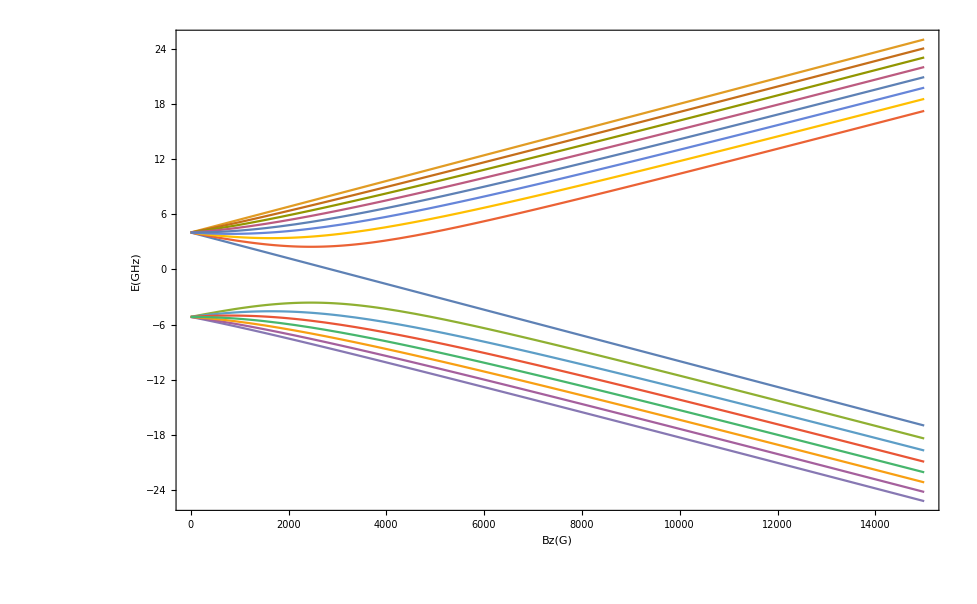

```mathematica
Plot[Evaluate[eval0/.hfc0],{Bz,0,15000},Frame->True,FrameLabel->{"Bz(G)","E(GHz)"}]
```

```mathematica
Clear[Ix,Iy,Iz,Jx,Jy,Jz]
```

Now for the D1 line, i.e. the level 6 P_(1/2), we still have J=1/2, and I=7/2. Then

```mathematica
Ix=KroneckerProduct[sx[7/2],id[1/2]];
```

```mathematica
Iy=KroneckerProduct[sy[7/2],id[1/2]];
```

```mathematica
Iz=KroneckerProduct[sz[7/2],id[1/2]];
```

```mathematica
Jx=KroneckerProduct[id[7/2],sx[1/2]];
```

```mathematica
Jy=KroneckerProduct[id[7/2],sy[1/2]];
```

```mathematica
Jz=KroneckerProduct[id[7/2],sz[1/2]];
```

```mathematica
Fx=Ix+Jx;Fy=Iy+Jy;Fz=Iz+Jz;
```

We observe down that the Hamiltonian is still the same but we need to rewrite the g-factors and the magnetic dipole constant.

```mathematica
Hhf1=A1(Ix.Jx+Iy.Jy+Iz.Jz)+μB*Bz*(gI*Iz+gJ1*Jz);
```

```mathematica
hfc1={μB->μBn,ℏ->ℏn,A1->Quantity["PlanckConstant"]*Quantity[291.920,"MHz"]/EnergyUnit,gJ1->0.66590,gI->−0.00039885395};
```

```mathematica
eval1=Eigenvalues[Hhf1]//FullSimplify;
```

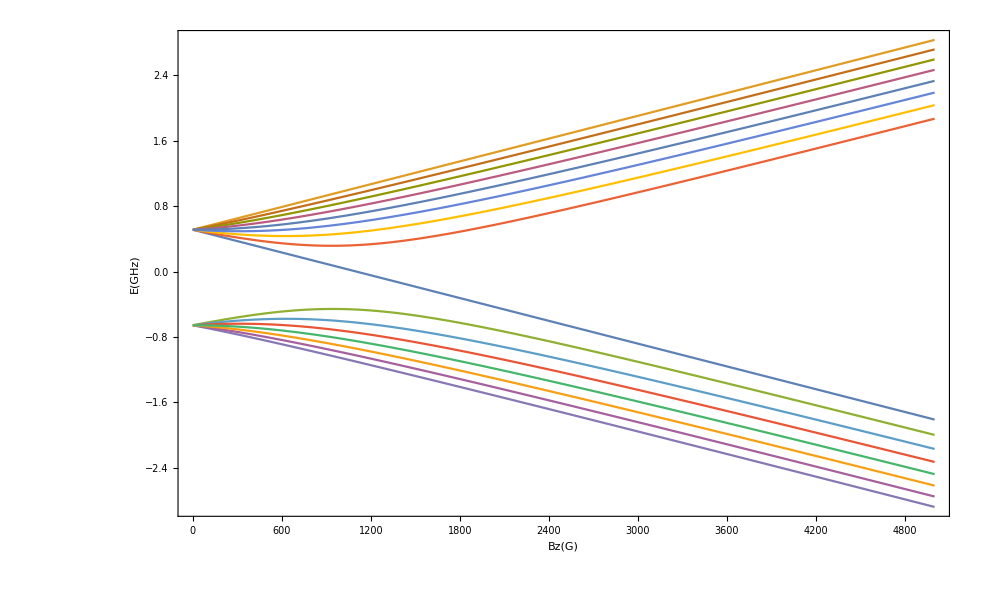

```mathematica
Plot[Evaluate[eval1/.hfc1],{Bz,0,5000},Frame->True,FrameLabel->{"Bz(G)","E(GHz)"}]
```

```mathematica
Clear[Ix,Iy,Iz,Jx,Jy,Jz]
```

Now for the D2 line, i.e. the level 6 P_(3/2), we have J=3/2, thus the basis for the description is:

```mathematica
Ix=KroneckerProduct[sx[7/2],id[3/2]];
```

```mathematica
Iy=KroneckerProduct[sy[7/2],id[3/2]];
```

```mathematica
Iz=KroneckerProduct[sz[7/2],id[3/2]];
```

```mathematica
Jx=KroneckerProduct[id[7/2],sx[3/2]];
```

```mathematica
Jy=KroneckerProduct[id[7/2],sy[3/2]];
```

```mathematica
Jz=KroneckerProduct[id[7/2],sz[3/2]];
```

```mathematica
Fx=Ix+Jx;Fy=Iy+Jy;Fz=Iz+Jz;
```

Since J>1/2 we considerate the quadrupole term in the interaction. Moreover, for this case we define the constants of the g-factors, and the dipole and quadrupole before computing the eigenvalues:

```mathematica
A2=Quantity["PlanckConstant"]*Quantity[50.273,"MHz"]/EnergyUnit;μB->μBn;B=Quantity["PlanckConstant"]*Quantity[-0.53,"MHz"]/EnergyUnit;gJ2=1.3340;gI=-0.00039885395;Is=7/2;J=3/2;
```

```mathematica
Hhf2=A2(Ix.Jx+Iy.Jy+Iz.Jz)+μB*Bz*(gI*Iz+gJ2*Jz)+B*((3(Ix.Jx+Iy.Jy+Iz.Jz)^2+3/2(Ix.Jx+Iy.Jy+Iz.Jz)-(Ix^2+Iy^2+Iz^2).(Jx^2+Jy^2+Jz^2))/(2*Is(2*Is-1)J(2*J-1)));
```

```mathematica
eval2=Eigenvalues[Hhf2]//Simplify;
```

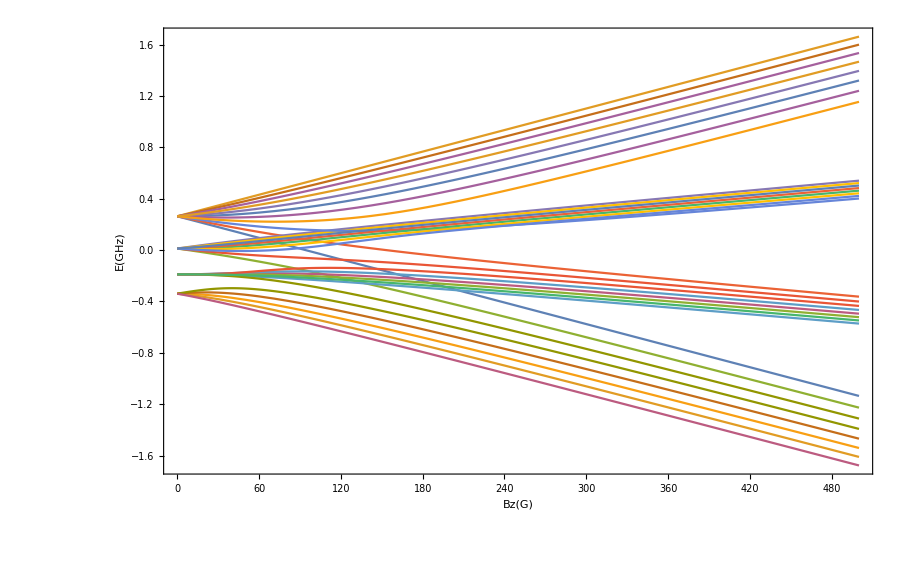

```mathematica
Plot[Evaluate[Re[eval2]],{Bz,0,500},Frame->True,FrameLabel->{"Bz(G)","E(GHz)"}]
```

```mathematica
Hhf2//Normal
```

```mathematica
Hhf2//Normal
```

{{0.263668+0.00279869 Bz,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.0879409+0.000931596 Bz,0.,0,0.115109,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.,-0.0879925-0.000935503 Bz,0.,0,0.132905,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.,-0.264132-0.0028026 Bz,0,0,0.115109,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.115109,0,0,0.188382+0.00279925 Bz,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.132905,0,0.,0.0628202+0.000932154 Bz,0.,0,0.150687,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.,0.,0.115109,0,0.,-0.0628465-0.000934945 Bz,0.,0,0.173977,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.,0.,0,0,0.,-0.188618-0.00280204 Bz,0,0,0.150687,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.,0.150687,0,0,0.113057+0.00279981 Bz,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.,0.,0.173977,0,0.,0.0376953+0.000932712 Bz,0.,0,0.168458,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.,0.,0.150687,0,0.,-0.0377048-0.000934387 Bz,0.,0,0.194493,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.,0.,0,0,0.,-0.113143-0.00280149 Bz,0,0,0.168458,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.,0.168458,0,0,0.0376953+0.00280037 Bz,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.,0.,0.194493,0,0.,0.0125661+0.00093327 Bz,0.,0,0.173977,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.,0.,0.168458,0,0.,-0.0125672-0.000933829 Bz,0.,0,0.200865,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,-0.0377048-0.00280093 Bz,0,0,0.173977,0.,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.,0.173977,0,0,-0.0377048+0.00280093 Bz,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.200865,0,0.,-0.0125672+0.000933829 Bz,0.,0,0.168458,0.,0.,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.173977,0,0.,0.0125661-0.00093327 Bz,0.,0,0.194493,0.,0.,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.0376953-0.00280037 Bz,0,0,0.168458,0.,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.168458,0,0,-0.113143+0.00280149 Bz,0.,0,0,0.,0.,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.194493,0,0.,-0.0377048+0.000934387 Bz,0.,0,0.150687,0.,0.,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.168458,0,0.,0.0376953-0.000932712 Bz,0.,0,0.173977,0.,0.,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.113057-0.00279981 Bz,0,0,0.150687,0.,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.150687,0,0,-0.188618+0.00280204 Bz,0.,0,0,0.,0.,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.173977,0,0.,-0.0628465+0.000934945 Bz,0.,0,0.115109,0.,0.,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.150687,0,0.,0.0628202-0.000932154 Bz,0.,0,0.132905,0.,0.},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.188382-0.00279925 Bz,0,0,0.115109,0.},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.115109,0,0,-0.264132+0.0028026 Bz,0.,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.132905,0,0.,-0.0879925+0.000935503 Bz,0.,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.115109,0,0.,0.0879409-0.000931596 Bz,0.},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.263668-0.00279869 Bz}}